# Выполнение расчетного задания по дисциплине Тепломассообмен в среде Mathematica 14 Студент: Азимова Зарина Группа: ТФ-11-22 Задача № 1 -Graphics-

#### Данные из условия: d2=100(mm);δ=3(mm) - геометрия труб ; tAir=5 (°C)-температура воздуха;tLiquid1=100(°C)-температура горячей воды на входе (как t_ж1) ; p=5(MPa)- давление горячей воды;w=0.2(m/s) - скорость течения горячей воды; λMinWool=0.05(W/m*K);δMinWool=50(mm); tLiquid2=100-20=80(°C)-температура горячей воды на выходе(как t_ж2) ; λConcrete=1.28(W/m K);δConcrete=50(mm);ϵ=0.8-излучательная способность поверхности материала труб; α= 12.8(W/m^2K)-коэффициент теплоотдачи

```mathematica
d2=100*10^-3;δ=3*10^-3;tAir=5;tLiquid1=100;p=5*10^6;w=0.2;λMinWool=0.05;δMinWool=50*10^-3;tLiquid2=80;λConcrete=1.28;δConcrete=50*10^-3;
ϵ=0.8;
α=12.8;
```

#### Сталь берем нержавеющую, ее коэффициент теплопроводности λSteel (W/m K) берем как const в виду слабой зависимости от температуры:

```mathematica
λSteel=14.4 ;
```

#### Изобарную (p=5MPa)теплоемкость и плотность воды при tLiquid1 и tLiquid2 найдем через REFPROP при substance-water cp: tLiquid1=100 (°C) =373.15(K) cp1=4.2024 (kJ/kg K) -Graphics-

#### tLiquid2=80 (°C) =353.15(K) cp2=4.2142 (kJ/kg K) -Graphics- плотность: tLiquid1=100 (°C) ρ1=960.64 (kg/m^3) -Graphics- tLiquid2=80 (°C) ρ2=974.05 (kg/m^3) -Graphics-

```mathematica
cp1=4.2024;cp2=4.2142  ;ρ1=960.64;ρ2=974.05 ;
```

#### Средняя удельная изобарная теплоемкость cpAverage(J/kg K)

```mathematica
cpAverage=(cp1+cp2)/2*1000
```

4208.3

#### Средняя плотность воды ρAverage (kg/m^3)

```mathematica
ρAverage=(ρ1+ρ2)/2
```

967.345

#### Массовый расход воды G(kg/s)

```mathematica
G=π*((d2-2*δ)/2)^2*w*ρAverage
```

1.34263

#### Найдем диаметры d1, d3 (m)

```mathematica
d1=d2-2δ//N
```

0.094

```mathematica
d3=d2+2δ//N
```

0.106

#### Найдем линейный коэффициент теплопередачи для трубы с ватной изоляцией KlinearMinWool (W/m K)

```mathematica
KlinearMinWool=1/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λMinWool)*Log[d3/d2]+1/(α*d3))
```

0.464472

#### Применяя формулу Шухова найдем расстояние(длину трубы) на котором будет выполняться условие разности температур на входе и выходе в трубу с изоляцией из минеральной ваты:

```mathematica
L=First[NSolveValues[tLiquid2==tAir+(tLiquid1-tAir)*Exp[-KlinearMinWool/(G*cpAverage)*π*x],x]]
```

915.337

#### Найдем линейный коэффициент теплопередачи для трубы с бетонной изоляцией KlinearConcrete (W/m K)

```mathematica
KlinearConcrete=1/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/(α*d3))
```

0.627725

#### По формуле Шухова найдем температуру на выходе из трубы с бетонной изоляцией:

```mathematica
t[x_,k_]:=tAir+(tLiquid1-tAir)*Exp[-k/(G*cpAverage)*π*x]
```

```mathematica
t[L,KlinearConcrete]
```

74.0204

#### Найдем линейный коэффициент теплопередачи для трубы без изоляции KlinearRaw (W/m K)

```mathematica
KlinearRaw=1/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(α*d3))
```

0.636824

#### По формуле Шухова найдем температуру на выходе из трубы без изоляции:

```mathematica
t[L,KlinearRaw]
```

73.7015

#### Функция теплового потока и плотности теплового потока :

```mathematica
Q[x_,k_]:=k*π*(t[x,k]-tAir)*x;
qLinear[x_,k_]:=k*π*(t[x,k]-tAir);
```

#### Тепловой поток Q(W) и его линейная плотность qLinear(W/m) для голой трубы:

```mathematica
Q[L,KlinearRaw]
```

125810.

```mathematica
qLinear[L,KlinearRaw]
```

137.447

#### Тепловой поток Q(W) и его линейная плотность qLinear(W/m) для трубы с бетонной изоляцией:

```mathematica
Q[L,KlinearConcrete]
```

124588.

```mathematica
qLinear[L,KlinearConcrete]
```

136.112

#### Тепловой поток Q(W) и его линейная плотность qLinear(W/m) для трубы с ватной изоляцией:

```mathematica
Q[L,KlinearMinWool]
```

100173.

```mathematica
qLinear[L,KlinearMinWool]
```

109.439

### Произведем расчеты по другому:

```mathematica
qLinearAdditional[k_]:=k*π*((tLiquid1+tLiquid2)/2-tAir)
```

#### Запишем баланс энергий: Q=qLinear*L=G*cpAverage*(tLiquid1-tLiquid2)=π *(d1/2)^2*w*cpAverage*ρAverage*(tLiquid1-tLiquid2),отсюда можно найти L(m):

```mathematica
Ladditional=First[NSolveValues[qLinearAdditional[KlinearMinWool]*x==π*(d1/2)^2*w*cpAverage*ρAverage*(tLiquid1-tLiquid2),x]]
```

911.099

#### Выразим tLiquid2 из линейной плотности теплового потока как переменную :

```mathematica
Solve[k*π*((tLiquid2asVariable+tLiquid1)/2-tAir)*x==π*(d1/2)^2*w*cpAverage*ρAverage*(tLiquid1-tLiquid2asVariable),tLiquid2asVariable]
```

{{tLiquid2asVariable→(565020.-141.372 k x)/(5650.2+1.5708 k x)}}

```mathematica
tLiquid2asVariable[k_,x_]:=(565019.8006215384-141.3716694115407 *k* x)/(5650.198006215384+1.5707963267948966* k* x)
```

#### Теперь найдем температуры на выходе из трубы с бетонной изоляцией и трубы без изоляции. Бетонная изоляция:

```mathematica
tLiquid2asVariable[KlinearConcrete,Ladditional]
```

73.9348

#### Голая труба:

```mathematica
tLiquid2asVariable[KlinearRaw,Ladditional]
```

73.6094

#### Изобразим функциональные зависимости температуры жидкости в точке χ, где χ-обобщенное расстояние(от точки входа воды)

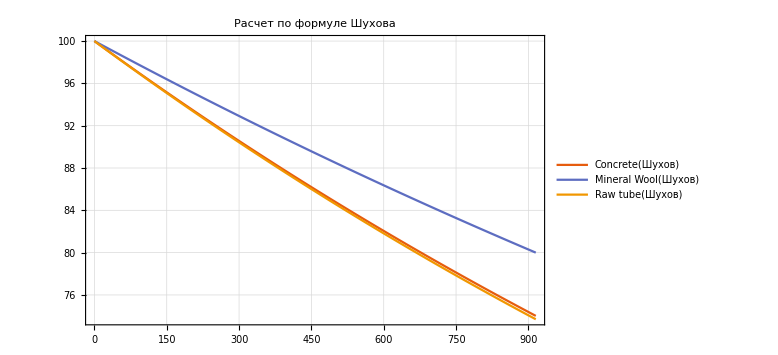

```mathematica
Plot[{t[χ,KlinearConcrete],t[χ,KlinearMinWool],t[χ,KlinearRaw]},{χ,0,L},PlotLabel->"Расчет по формуле Шухова",PlotTheme->"Scientific",PlotLegends->{"Concrete(Шухов)","Mineral Wool(Шухов)","Raw tube(Шухов)"},ImageSize->Large,GridLines->Automatic]
```

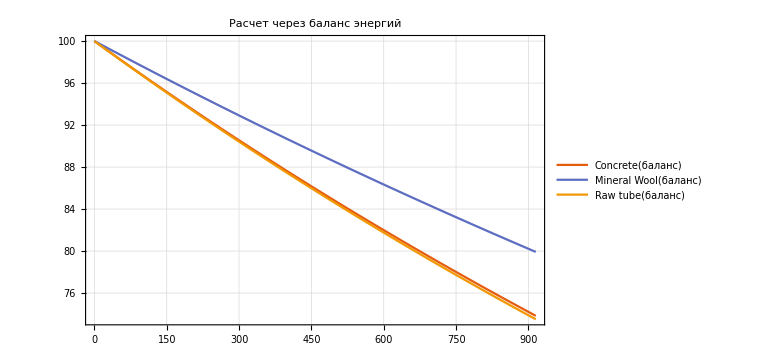

```mathematica
Plot[{tLiquid2asVariable[KlinearConcrete,χ],tLiquid2asVariable[KlinearMinWool,χ],tLiquid2asVariable[KlinearRaw,χ]},{χ,0,L},PlotLabel->"Расчет через баланс энергий",PlotTheme->"Scientific",PlotLegends->{"Concrete(баланс)","Mineral Wool(баланс)","Raw tube(баланс)"},ImageSize->Large,GridLines->Automatic]
```

#### Сопоставим функции температур в одной системе координат:

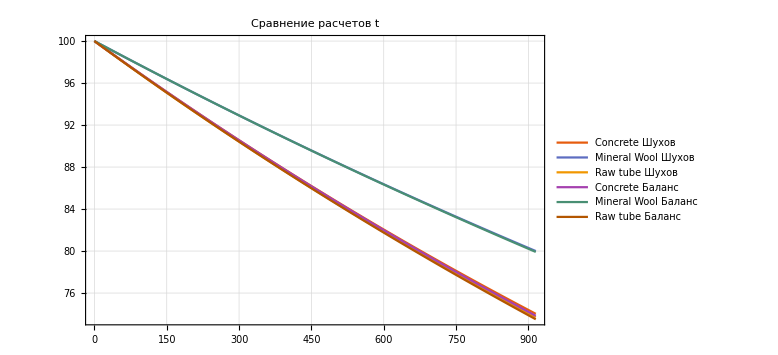

```mathematica
Plot[{t[χ,KlinearConcrete],t[χ,KlinearMinWool],t[χ,KlinearRaw],tLiquid2asVariable[KlinearConcrete,χ],tLiquid2asVariable[KlinearMinWool,χ],tLiquid2asVariable[KlinearRaw,χ]},{χ,0,L},PlotLabel->"Сравнение расчетов t",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Баланс","Mineral Wool Баланс","Raw tube Баланс"},ImageSize->Large,GridLines->Automatic]
```

#### Точно так же изобразим функции линейных плотностей тепловых потоков. Для начала введем функцию линейной плотности теплового потока при расчете методом баланса энергий:

```mathematica
qLinearAdditionalFunction[k_]:=k*π*((tLiquid1-tLiquid2)/2-tAir)
```

#### Покажем графики линейных плотностей тепловых потоков в одной координатной плоскости ql(W/m):

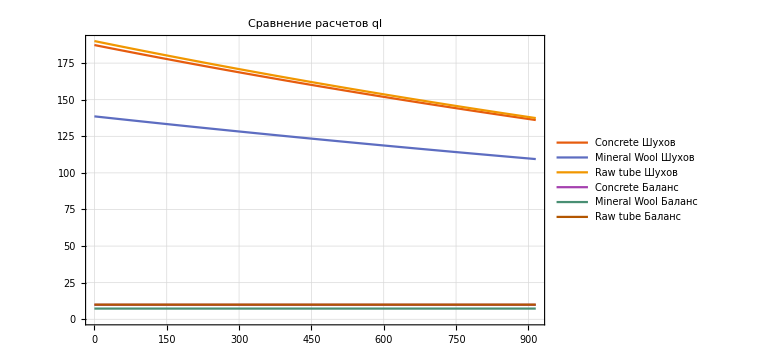

```mathematica
Plot[{qLinear[χ,KlinearConcrete],qLinear[χ,KlinearMinWool],qLinear[χ,KlinearRaw],qLinearAdditionalFunction[KlinearConcrete],qLinearAdditionalFunction[KlinearMinWool],qLinearAdditionalFunction[KlinearRaw]},{χ,0,L},PlotLabel->"Сравнение расчетов ql",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Баланс","Mineral Wool Баланс","Raw tube Баланс"},ImageSize->Large,GridLines->Automatic]
```

#### Теперь построим поверхностные плотности тепловых потоков qc (W/m^2):

```mathematica
qcShuhov[x_,k_]:=qLinear[x,k]/(π*d1);qcBalance[k_]:=qLinearAdditionalFunction[k]/(π*d1);
```

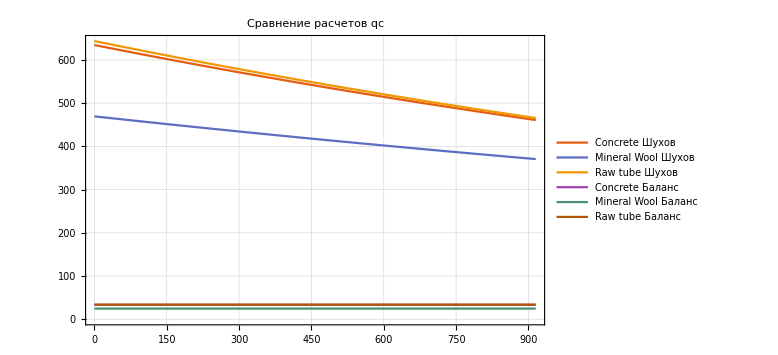

```mathematica
Plot[{qcShuhov[χ,KlinearConcrete],qcShuhov[χ,KlinearMinWool],qcShuhov[χ,KlinearRaw],qcBalance[KlinearConcrete],qcBalance[KlinearMinWool],qcBalance[KlinearRaw]},{χ,0,L},PlotLabel->"Сравнение расчетов qc",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Баланс","Mineral Wool Баланс","Raw tube Баланс"},ImageSize->Large,GridLines->Automatic]
```

#### Найдем среднее значение линейной плотности теплового потока(W/m):

```mathematica
qLinearAverageWithoutInsulation=(qLinear[0,KlinearRaw]+qLinear[L,KlinearRaw])/2
```

163.754

```mathematica
qLinearAverageConcreteInsulation=(qLinear[0,KlinearConcrete]+qLinear[L,KlinearConcrete])/2
```

161.729

```mathematica
qLinearAverageMinWoolInsulation=(qLinear[0,KlinearMinWool]+qLinear[L,KlinearMinWool])/2
```

124.03

#### Среднее значение температуры на поверхности труб:

```mathematica
{twWithoutIns,twConcreteIns,twMinWoolIns}=Flatten[NSolveValues[{qLinearAverageWithoutInsulation==π*(twWithoutInsBUFFER-tAir)/(1/(α*d2)),qLinearAverageConcreteInsulation==π*(twConcreteInsBUFFER-tAir)/(1/(α*d3)),qLinearAverageMinWoolInsulation==π*(twMinWoolInsBUFFER-tAir)/(1/(α*d3))},{twWithoutInsBUFFER,twConcreteInsBUFFER,twMinWoolInsBUFFER}]]
```

{45.7223,42.9421,34.098}

#### Учтем излучение σ- константа Стефана-Больцмана(W/m^2 K^4)

```mathematica
σ=5.671*10^-8;
```

#### Переведем температуры на поверхности труб и температуру воздуха в абсолютные единицы(Кельвины)

```mathematica
TwWithoutIns=twWithoutIns+273.15;TwConcreteIns=twConcreteIns+273.15;TwMinWoolIns=twMinWoolIns+273.15;Tair=tAir+273.15;
```

#### Найдем результирующую плотность потока излучения Eres(W/m^2):

```mathematica
EresMinWool=ϵ*σ*(TwMinWoolIns^4-Tair^4)
```

132.742

```mathematica
EresConcrete=ϵ*σ*(TwConcreteIns^4-Tair^4)
```

181.342

```mathematica
EresWithoutIns=ϵ*σ*(TwWithoutIns^4-Tair^4)
```

197.487

#### Найдем эквивалентный коэффициент теплоотдачи излучением αEqv (W/m^2K):

```mathematica
αEqvMinWool=EresMinWool/(TwMinWoolIns-Tair)
```

4.56189

```mathematica
αEqvConcrete=EresConcrete/(TwConcreteIns-Tair)
```

4.77944

```mathematica
αEqvWithoutIns=EresWithoutIns/(TwWithoutIns-Tair)
```

4.84961

```mathematica
MradMinWool=1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λMinWool)*Log[d3/d2]+1/((α+αEqvMinWool)*d3)
```

1.95933

```mathematica
MradConcrete=1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvConcrete)*d3)
```

1.39267

```mathematica
MradWithoutIns=1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/((α+αEqvWithoutIns)*d3)
```

1.36778

```mathematica
P=(d1/2)^2*w*ρAverage*cpAverage
```

1798.51

```mathematica
tLiquid2RadiationVariable[M_,x_]:=(2*P*M*tLiquid1+2*tAir*x - tLiquid1*x)/(x+2*P*M)
```

#### Линейная плотность потока излучения для трубы с ватной изоляцией:

```mathematica
qLinearRadiationMinWool[x_]:=π*((tLiquid1+tLiquid2RadiationVariable[MradMinWool,x])/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvMinWool)*d3))
```

#### Из баланса энергий найдем длину трубы:

```mathematica
LwithRadiation=First[NSolveValues[((tLiquid1+tLiquid2)/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvMinWool)*d3))*Len ==π*(d1/2)^2*w*ρAverage*cpAverage*(tLiquid1-tLiquid2),Len]]
```

1860.44

#### Линейная плотность потока излучения трубы с ватной изоляцией:(W/m)

```mathematica
qLinearRadiationMinWool[LwithRadiation]
```

168.73

#### Для трубы без изоляции:(W/m)

```mathematica
qLinearRadiationWithoutIns[x_]:=π*((tLiquid1+tLiquid2RadiationVariable[MradWithoutIns,x])/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/((α+αEqvWithoutIns)*d3))
```

```mathematica
qLinearRadiationWithoutIns[LwithRadiation]
```

158.33

```mathematica
tLiquid2RadiationVariableWithoutIns=tLiquid2RadiationVariable[MradWithoutIns,LwithRadiation]
```

47.8667

#### Для трубы с изоляцией из бетона:

```mathematica
qLinearRadiationConcrete[x_]:=π*((tLiquid1+tLiquid2RadiationVariable[MradConcrete,x])/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvConcrete)*d3))
```

```mathematica
qLinearRadiationConcrete[LwithRadiation]
```

156.266

```mathematica
tLiquid2RadiationVariable[MradConcrete,LwithRadiation]
```

48.5462

#### Рассчитаем потери теплоты:

```mathematica
QradConcrete[x_]:=qLinearRadiationConcrete[x]*x;
QradMinWool[x_]:=qLinearRadiationMinWool[x]*x;
QradWithoutIns[x_]:=qLinearRadiationWithoutIns[x]*x;
```

#### Потери теплоты в трубе с бетонной изоляцией:(W)

```mathematica
QradConcrete[LwithRadiation]
```

290724.

#### Потери теплоты в трубе с ватной изоляцией:(W)

```mathematica
QradMinWool[LwithRadiation]
```

313913.

```mathematica
QradWithoutIns[LwithRadiation]
```

294564.

#### Сравним расчеты температуры(Шухов/Излучение):

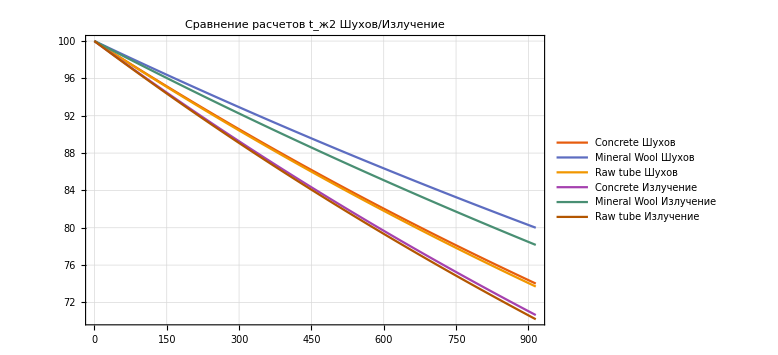

```mathematica
Plot[{t[χ,KlinearConcrete],t[χ,KlinearMinWool],t[χ,KlinearRaw],tLiquid2RadiationVariable[MradConcrete,χ],tLiquid2RadiationVariable[MradMinWool,χ],tLiquid2RadiationVariable[MradWithoutIns,χ]},{χ,0,L},PlotLabel->"Сравнение расчетов t_(:04362) Шухов/Излучение",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Излучение","Mineral Wool Излучение","Raw tube Излучение"},ImageSize->Large,GridLines->Automatic]
```

#### Сравним расчеты линейной плотности потоков тепла/излучения(Шухов/Излучение):

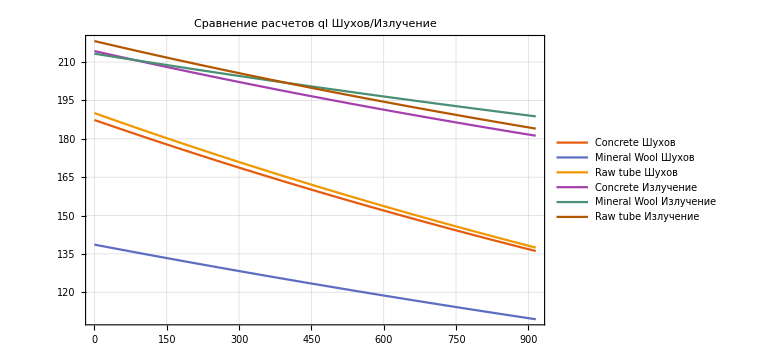

```mathematica
Plot[{qLinear[χ,KlinearConcrete],qLinear[χ,KlinearMinWool],qLinear[χ,KlinearRaw],qLinearRadiationConcrete[χ],qLinearRadiationMinWool[χ],qLinearRadiationWithoutIns[χ]},{χ,0,L},PlotLabel->"Сравнение расчетов ql Шухов/Излучение",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Излучение","Mineral Wool Излучение","Raw tube Излучение"},ImageSize->Large,GridLines->Automatic]
```

#### Соберем все результаты выше воедино. Способ основанный на формуле Шухова. Температуры жидкости на выходе(°C):(порядок:бетон,вата,без изоляции)

```mathematica
t[L,KlinearConcrete]
```

74.0204

```mathematica
t[L,KlinearMinWool]
```

80.

```mathematica
t[L,KlinearRaw]
```

73.7015

#### Тепловой поток(W):(порядок:бетон,вата,без изоляции)

```mathematica
Q[L,KlinearConcrete]
```

124588.

```mathematica
Q[L,KlinearMinWool]
```

100173.

```mathematica
Q[L,KlinearRaw]
```

125810.

#### Способ основанный на методе баланса энергии. Температуры жидкости на выходе(°C):(порядок:бетон,вата,без изоляции).

```mathematica
tLiquid2asVariable[KlinearConcrete,Ladditional]
```

73.9348

```mathematica
tLiquid2asVariable[KlinearMinWool,Ladditional]
```

80.

```mathematica
tLiquid2asVariable[KlinearRaw,Ladditional]
```

73.6094

#### Тепловой поток(W):(порядок:бетон,вата,без изоляции)

```mathematica
Qadditional[k_,x_]:=qLinear[x,k]*x;
```

```mathematica
Qadditional[KlinearConcrete,Ladditional]
```

124195.

```mathematica
Qadditional[KlinearMinWool,Ladditional]
```

99818.6

```mathematica
Qadditional[KlinearRaw,Ladditional]
```

125416.

#### Способ с учетом излучения.Температуры жидкости на выходе(°C):(порядок:бетон,вата,без изоляции)

```mathematica
tLiquid2RadiationVariable[MradConcrete,LwithRadiation]
```

48.5462

```mathematica
tLiquid2RadiationVariable[MradMinWool,LwithRadiation]
```

60.3192

```mathematica
tLiquid2RadiationVariable[MradWithoutIns,LwithRadiation]
```

47.8667

#### Поток излучения(W):(порядок:бетон,вата,без изоляции)

```mathematica
QradConcrete[LwithRadiation]
```

290724.

```mathematica
QradMinWool[LwithRadiation]
```

313913.

```mathematica
QradWithoutIns[LwithRadiation]
```

294564.

#### Найдем критический диаметр при бетонной и ватной изоляциях

```mathematica
d2//N
```

0.1

```mathematica
dCriticalConcrete=d2+(2λConcrete)/α
```

0.3

```mathematica
dCriticalMinWool=d2+(2λMinWool)/α
```

0.107813

#### Вывод: Тепло от теплоносителя лучше всего сохраняет труба с ватной изоляцией. На втором месте бетон. На почетном третьем- труба без изоляции